```mathematica
Exit[]
```

```mathematica
u[x_]:=Max[0,1-Exp[-x]]
```

```mathematica
g[f_,p_,s_]:=p u[f+s]+(1-p) u[(f p)/(p-1)+s]
```

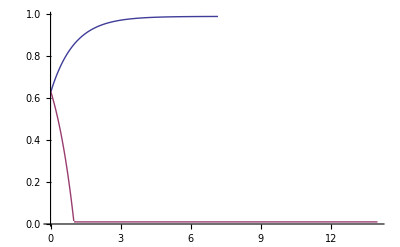

```mathematica
p=.99;Plot[{g[f ,p,1],g[-f,p,1]},{f,0,14},PlotRange->All]
```